```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["16_cv.dat","Table"];
MagnetData = Import["16_magnetization.dat","Table"];
SusceptData = Import["16_susceptibility.dat","Table"];
```

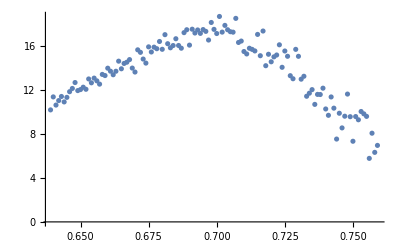

```mathematica
ListPlot[Take[SusceptData,{340, 460}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{340,460}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,16},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{17.1316 ⅇ^(-191.586 (-0.693542+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 17.1316 | 0.138443 | 123.744 | 9.84081×10^-127
Sigma | 0.0510861 | 0.000880794 | 58.0001 | 1.39805×10^-88
mu | 0.693542 | 0.000556754 | 1245.69 | 7.01301×10^-245}

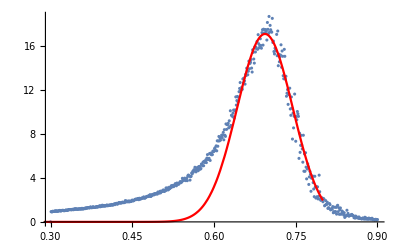

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

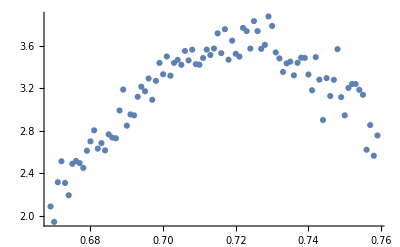

```mathematica
ListPlot[Take[CvData,{370,460}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{370,450}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{{A,3.6},Sigma,mu},x]
```

FittedModel[3.62969 ⅇ^(-193.748 (-«19»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{3.62969 ⅇ^(-193.748 (-0.721382+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 3.62969 | 0.0212266 | 170.997 | 3.37686×10^-102
Sigma | 0.0508002 | 0.00128742 | 39.459 | 2.68664×10^-53
mu | 0.721382 | 0.000746721 | 966.067 | 8.20812×10^-161}

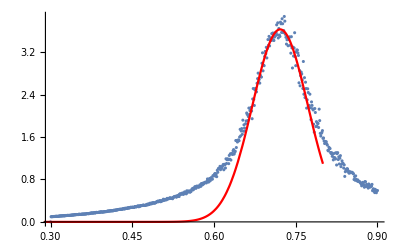

```mathematica
Show[ListPlot[CvData],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```